```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=100;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

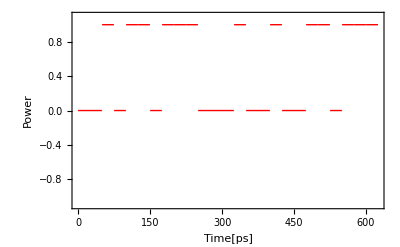

-Graphics-

Cos[400 π t]

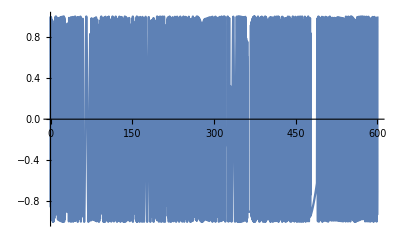

Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0])

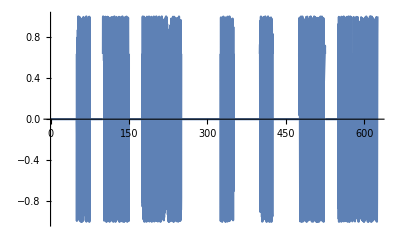

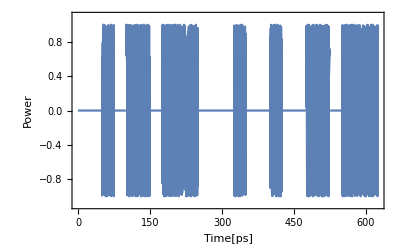

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
bit=25;
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25<t<(i+1)*25,1,0],If[i*25<t<(i+1)*25,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
Plot[signal[t],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]

Fc= 200 ;(*搬送波の周波数[THz]*)
carrier[t]= Cos[2*Pi*Fc*t]
Plot[carrier[t], {t,0,600}]
cs[t]=signal[t]*carrier[t]
Plot[Evaluate[cs[t]],{t,0,bit*25}]
Plot[Evaluate[cs[t]],{t,0,bit*25},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
```

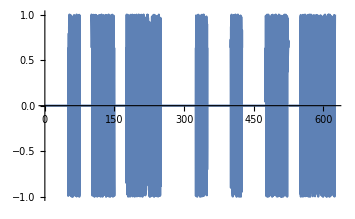

-Graphics-

```mathematica
-Graphics-
Evaluate[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
ComplexExpand[Integratepaclet:ref/Integrate[cs[t]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,625}]]
```

-Graphics-

∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1

Rule::rhs: パターンpaclet:ref/Integrateは規則System`ComplexExpandDump`reimexpr[RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) «1» (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+«19»+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),«1»]]→«1»の右辺にあります．

RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),{t,0,625}]

```mathematica
FourierTransform[cs[t],t,ω*10^{-12}]
(*Cs(ω)=ComplexExpand[FourierTransform[cs[t],t,ω]]*)
Cs[ω]:=1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω])
Re[Cs[ω]]
(*Plot[Re[FourierTransform[cs[t],t,ω]],{ω,-100,100}]*)
(*Plot[Evaluate[[Re[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]]],{f,-100,100}]*)
```

FourierTransform[Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),t,{ω/1000000000000}]

1/(√(2 π))Re[1/(-160000 π^2+ω^2)ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω])]

-Graphics-

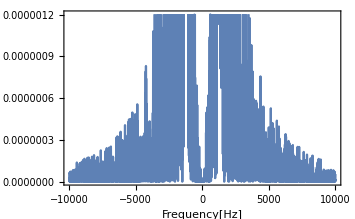

```mathematica
-Graphics-
Plot[(Re[Cs[ω]]^2+Im[Cs[ω]]^2),{ω,-10^4,10^4},Frame->True,FrameLabel->{"Frequency[Hz]","Power"},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
∫_0^(bit*25*10^-12) signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

0

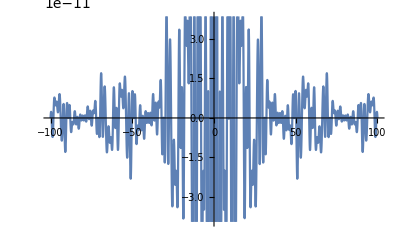

```mathematica
fc[f_]:=-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))(*-1/(2 f π)ⅈ ⅇ^(-(49 ⅈ f π)/10000000000) (-1+ⅇ^((3 ⅈ f π)/10000000000)-ⅇ^((ⅈ f π)/2500000000)+ⅇ^((3 ⅈ f π)/5000000000)-ⅇ^((7 ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/1250000000)-ⅇ^((9 ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/1000000000)-ⅇ^((3 ⅈ f π)/2500000000)+ⅇ^((19 ⅈ f π)/10000000000)-ⅇ^((21 ⅈ f π)/10000000000)+ⅇ^((11 ⅈ f π)/5000000000)-ⅇ^((ⅈ f π)/400000000)+ⅇ^((13 ⅈ f π)/5000000000)-ⅇ^((27 ⅈ f π)/10000000000)+ⅇ^((7 ⅈ f π)/2500000000)-ⅇ^((29 ⅈ f π)/10000000000)+ⅇ^((3 ⅈ f π)/1000000000)-ⅇ^((33 ⅈ f π)/10000000000)+ⅇ^((17 ⅈ f π)/5000000000)-ⅇ^((7 ⅈ f π)/2000000000)+ⅇ^((9 ⅈ f π)/2500000000)-ⅇ^((37 ⅈ f π)/10000000000)+ⅇ^((39 ⅈ f π)/10000000000)-ⅇ^((ⅈ f π)/250000000)+ⅇ^((41 ⅈ f π)/10000000000)-ⅇ^((21 ⅈ f π)/5000000000)+ⅇ^((11 ⅈ f π)/2500000000)-ⅇ^((9 ⅈ f π)/2000000000)+ⅇ^((97 ⅈ f π)/20000000000))*)
Plot[Re[fc[f*10^9]],{f,-100,100}]
```

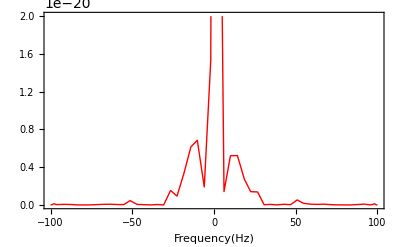

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

```mathematica
H_dis[ω]=Exp[-1/2*I(ω-2*Pi*Fc)^2*β2*L]
(*FourierTransform[Exp[-1/2*I(ω-2*Pi*Fc)^2*β2*L]*1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω]),ω,t,FourierParameters->{1,-1}]*)
```

ⅇ^((0.-1.01965×10^-21 ⅈ) (-400 π+ω)^2)

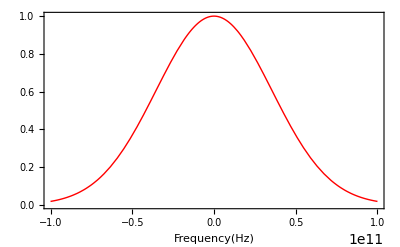

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

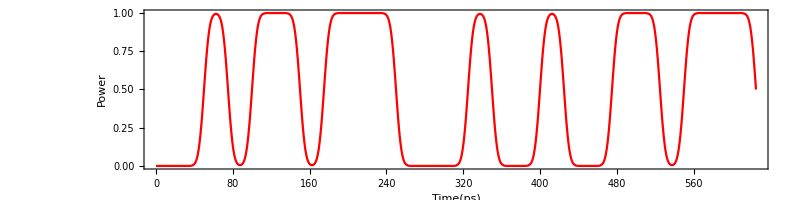

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]
```

```mathematica
(*For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
(*ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

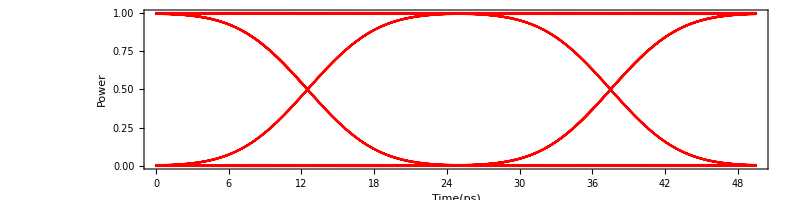

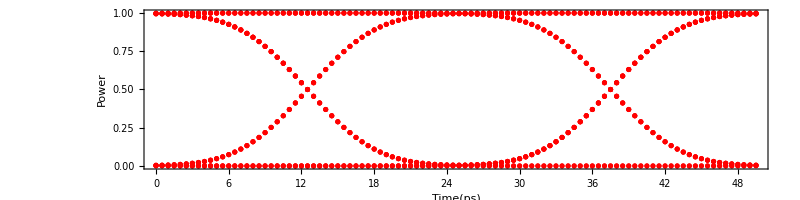

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
ListPlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

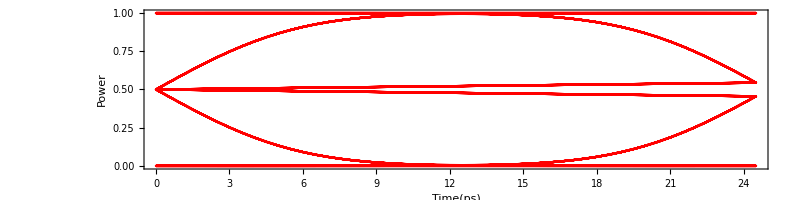

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,25]]
Table[eyetime[m],{m,0,25*bit,samp}];
eyebf=Table[{eyetime[m],nrzsig2[m]},{m,0,25*bit,samp}];
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

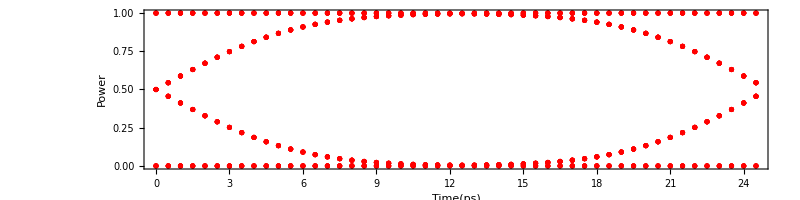

```mathematica
ListPlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

```mathematica
(*ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```